```mathematica
fD1 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D1_v1.csv"];
fD2 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D2_v1.csv"];
```

```mathematica
fD2 = Flatten@fD2;
fD1 = Flatten@fD1;
```

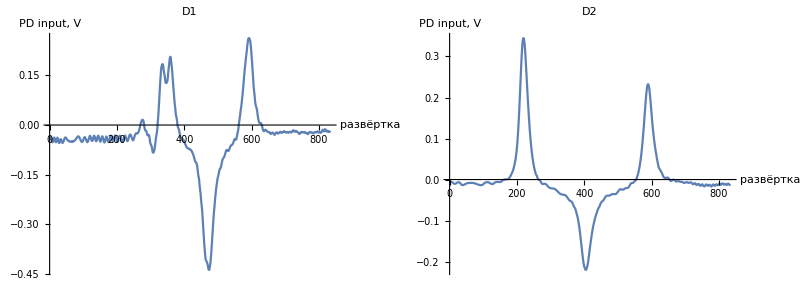

D:\Kami\git_folder\notes_5sem\rqc\data_processing_1\D12.pdf

```mathematica
scale = 240;
image = Multicolumn[{
ListPlot[fD1, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D1", AxesLabel->{"развёртка", "PD input, V"}],
ListPlot[fD2, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D2", AxesLabel->{"развёртка", "PD input, V"}]
}]
Export[NotebookDirectory[]<>"D12.pdf", image]
```